## Introduction

Source code for “Solvable model of non-identical swarmalators”

## Main simulation

### Simulation

#### Dynamic video (plot results as they are generated)

```mathematica
{dt,n1,T}={0.25,500,200};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={5,7,1};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
Dynamic[results]
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
results=plotResults[znew]
];
```

#### Static (plot results at end )

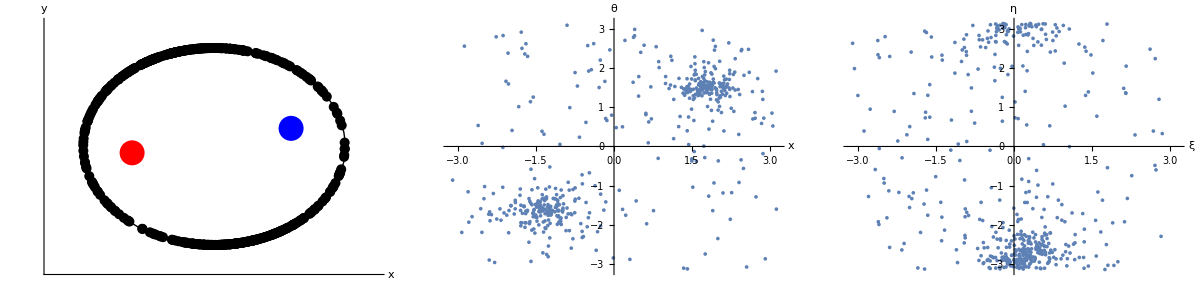

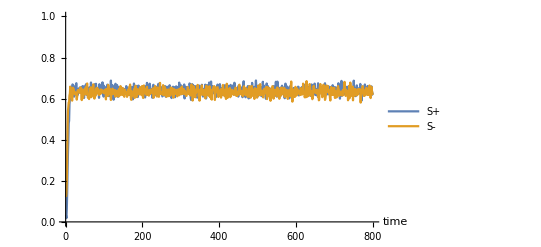

```mathematica
{dt,n1,T}={0.25,500,200};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={5,7,1}; 
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
results=plotResults[znew]
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

## Catalog of states

### Sync (double cluster)

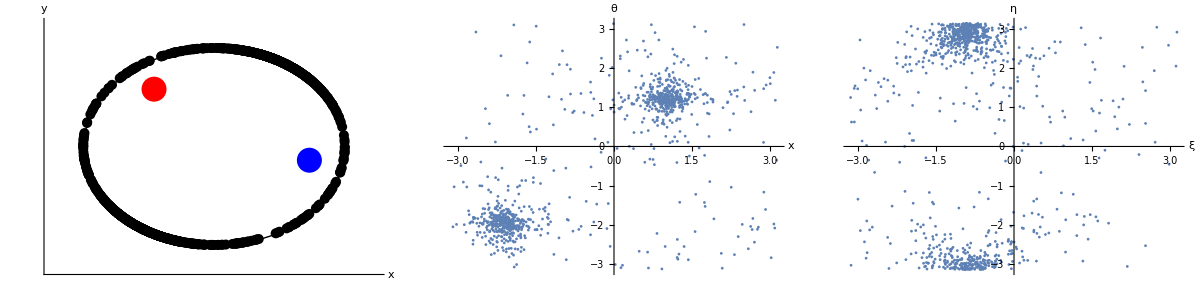

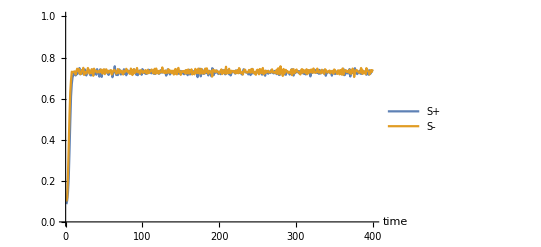

```mathematica
{dt,n1,T}={0.25,1000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={8,9,1}; 
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
results=plotResults[znew]
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

### Sync (single cluster -- IC different)

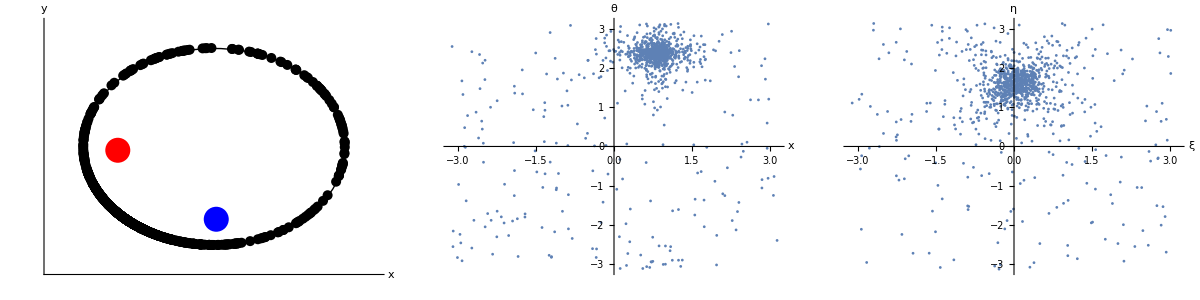

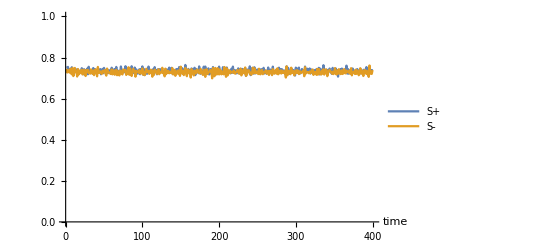

```mathematica
{dt,n1,T}={0.25,1000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={8,9,1}; 
{z0,znew}={Table[RandomReal[{0,0.5π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
results=plotResults[znew]
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

### Phase wave

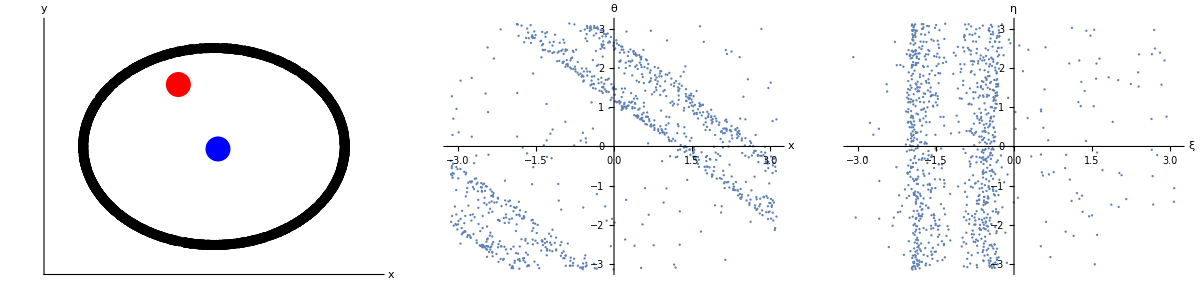

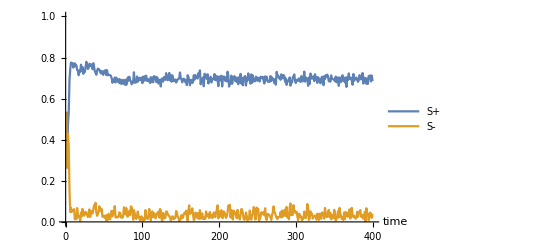

```mathematica
{dt,n1,T}={0.25,1000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={1,40,1}; 
{z0,znew}={Table[RandomReal[{0,0.5π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
results=plotResults[znew]
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

### Async

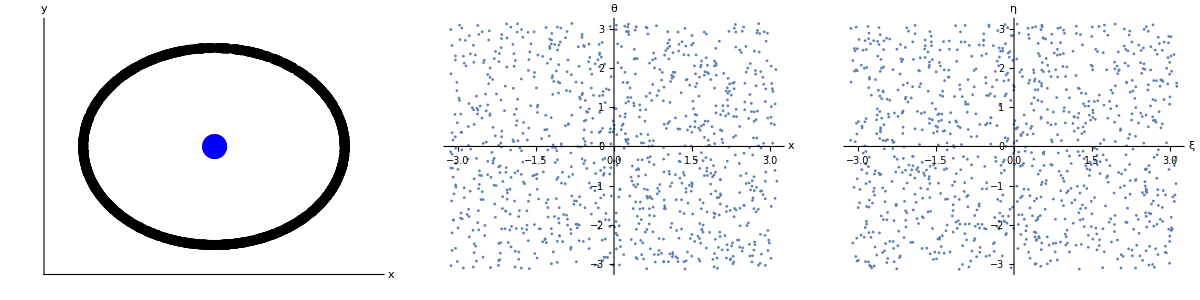

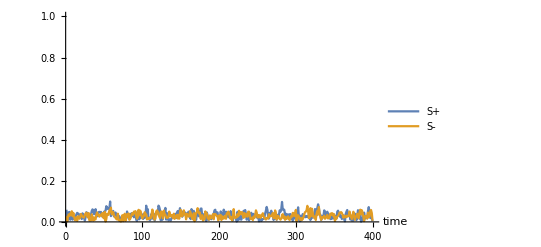

```mathematica
{dt,n1,T}={0.25,1000,100};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={1,1,1}; 
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
omega=RandomVariate[CauchyDistribution[0,Δ],n1];
nu=RandomVariate[CauchyDistribution[0,Δ],n1];
results={};
{Wps,Wms}={{},{}};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
results=plotResults[znew]
ListPlot[{Wps,Wms}//Abs,Joined->True,PlotRange->{0,1},AxesLabel->{Style["time",15]},PlotLegends->{Style["S+",15],Style["S-",13]}]
```

## Make movies

### Methods

Code below drawn the Lorenztian ω and ν deterministically: we projected linearly spaced [0, Δ] and then projected this using the inverse CDF of the Lorentzian. See code for details. The purpose was to create a ‘symmetric’ (v, ω) distribution; if we drew them randomly, the mean ω and ν were never quite zero, which led to an (unphysical; in the sense of a finite effect) drift in the phases of the order paramters Φ_±

```mathematica
makeOmegaNuSample[n_]:=Block[{omega1,n1,omegaTemp,nu1},
n1=√n;
omegaTemp=Table[Tan[(π/2)(2i−n1−1)/(n1+1)],{i,1,n1}];
omega1=Flatten[Table[omegaTemp,{i,1,√n}]]//N;
nu1=Flatten[Table[omegaTemp[[j]],{j,1,√n},{i,1,√n}]]//N;
Return[{omega1,nu1}]
];

plotResultsCustom[z_,J_,K_,Δ_,label_]:=Block[{colors,Wp,Wm,p1,p2,p3},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];
p1=Graphics[{

(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],
Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],
Black,Circle[{0,0},1]

},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium,PlotLabel->Style[label,15,Black]];
p2=ListPlot[{z[[1,All]]//mod,z[[2,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=ListPlot[{z[[1,All]]+z[[2,All]],z[[1,All]]-z[[2,All]]}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];
Return[Grid[{{p1,p2,p3}}]
]
];

plotResultsSingle[z_,J_,K_,Δ_,label_]:=Block[{colors,Wp,Wm,p1,p2,p3},
p2=ListPlot[{z[[1,All]]//mod,z[[2,All]]//mod}ᵀ,
PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},PlotLabel->Style[label,15,Black]];
Return[p2]
];
```

### Movies

#### Sync: two cluster

```mathematica
(*Make slides*)
{dt,n1,T}={0.1,900,10};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={8,9,1};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
{omega,nu}=makeOmegaNuSample[n1];
results={};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
fig=plotResultsCustom[znew,J,k,Δ,"Sync (two cluster): (J,K, Δ) = "<>ToString[{J,k,Δ}]];
AppendTo[slides,fig]
];

(*Make movei*)
SetDirectory[NotebookDirectory[]];
Export["sync-two-cluster.mov",slides]
```

sync-two-cluster.mov

#### Sync: one cluster

```mathematica
(*Make slides*)
{dt,n1,T}={0.1,900,10};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={8,9,1};   
{z0,znew}={Table[RandomReal[{0,0.5π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
{omega,nu}=makeOmegaNuSample[n1];
results={};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
fig=plotResultsCustom[znew,J,k,Δ,"Sync (one cluster): (J,K, Δ) = "<>ToString[{J,k,Δ}]];
AppendTo[slides,fig]
];

(*Make movei*)
SetDirectory[NotebookDirectory[]];
Export["sync-one-cluster.mov",slides]
```

sync-one-cluster.mov

#### Phase wave

```mathematica
(*Make slides*)
{dt,n1,T}={0.1,900,10};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={1,40,1};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
{omega,nu}=makeOmegaNuSample[n1];
results={};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
fig=plotResultsCustom[znew,J,k,Δ,"Phase wave: (J,K, Δ) = "<>ToString[{J,k,Δ}]];
AppendTo[slides,fig]
];

(*Make movei*)
SetDirectory[NotebookDirectory[]];
Export["phase-wave.mov",slides]
```

phase-wave.mov

#### Async

```mathematica
(*Make slides*)
{dt,n1,T}={0.1,900,10};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ}={1,1,1};   
{z0,znew}={Table[RandomReal[{0,2π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
{omega,nu}=makeOmegaNuSample[n1];
results={};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
{xs,θs}={{},{}};
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
AppendTo[xs,z0[[1,All]]];AppendTo[θs,z0[[2,All]]];
z0=znew;t++;
{Wp,Wm}=findWs[znew];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
fig=plotResultsCustom[znew,J,k,Δ,"Async: (J,K, Δ) = "<>ToString[{J,k,Δ}]];
AppendTo[slides,fig]
];

(*Make movei*)
SetDirectory[NotebookDirectory[]];
Export["async.mov",slides]
```

async.mov

#### All states at once

First make slides for all states

```mathematica
pars={{8,9,1,2,"sync (two cluster)"},{8,9,1,0.5,"sync (one cluster)"},{1,40,1,2,"phase wave"},{1,1,1,2,"async"}};
allSlides=ParallelTable[
(*Make slides*)
{dt,n1,T}={0.1,900,10};  (*dt = timestep, n = number of swarmalators*)
{J,k,Δ,ic,state}=par;   
{z0,znew}={Table[RandomReal[{0,ic π}],{i,1,2},{j,1,n1}],ConstantArray[0,{2,n1}]};
{omega,nu}=makeOmegaNuSample[n1];
results={};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,J,k,omega,nu];
z0=znew;t++;
fig=plotResultsSingle[znew,J,k,Δ,state<>": (J,K, Δ) = "<>ToString[{J,k,Δ}]];
AppendTo[slides,fig]
];
slides,
{par,pars}
];
```

Then sandwich them together and save

```mathematica
SetDirectory[NotebookDirectory[]];
fullSlides=Table[Grid[{allSlides[[1;;2,t]],allSlides[[3;;4,t]]}],{t,1,Dimensions[allSlides][[2]]}];
Export["movies/all-states.mov",fullSlides]
```

movies/all-states.mov

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{k,_Real},{omega,_Real,1},{nu,_Real,1}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J*Sin[xji] Cos[thetaji];
thetatemp=k*Sin[thetaji] Cos[xji];
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=thetatemp;vel[[2,j]]+=-thetatemp;
];
vel[[1,i]]=nu[[i]]+vel[[1,i]]/n;
vel[[2,i]]=omega[[i]]+vel[[2,i]]/n;
];
vel
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
]

plotResults[z_]:=Block[{colors,Wp,Wm,p1,p2,p3},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];
p1=Graphics[{

(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],
Cyan,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Magenta,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],
Black,Circle[{0,0},1]

},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];
p2=ListPlot[{z[[1,All]]//mod,z[[2,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=ListPlot[{z[[1,All]]+z[[2,All]],z[[1,All]]-z[[2,All]]}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];
Return[Grid[{{p1,p2,p3}}]
]
];

plotResults1DB[z_]:=Block[{colors},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
Return[ListPlot[{z[[1,All]],z[[2,All]]}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium]]
];

eulerStep[z_,F_,dt_,J_,k_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_,omega_,nu_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k,omega,nu];
k2=F[z+dt/2 k1,n,J,k,omega,nu];
k3=F[z+dt/2 k2,n,J,k,omega,nu];
k4=F[z+dt k3,n,J,k,omega,nu];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findGamma[xs_,θs_,cutoff_]:=Block[{gammas,i,n,x,θ,xSteady,rangeSteadyX,gammaX,θSteady,rangeSteadyθ,gammaθ,index},
(*Find fraction of swarmalators that have completed at least 
 one full oscillation (0,2π) mod 2π, after transients have been discarded *)

n= Dimensions[xs][[2]];
gammas={};
For[i=1,i≤n,i++,
{x,θ}={xs[[All,i]],θs[[All,i]]};

(*Check for one loop when x has approximately achieved its steady state*)
xSteady=x[[cutoff;;-1]];
rangeSteadyX=Max[xSteady]-Min[xSteady];
gammaX=If[rangeSteadyX>=2π,1,0];

(*Check for one loop when θ has approximately achieved its steady state*)
θSteady=θ[[cutoff;;-1]];
rangeSteadyθ=Max[θSteady]-Min[θSteady];
gammaθ=If[rangeSteadyθ>=2π,1,0];

(*Require both to be true*)
AppendTo[gammas,gammaX*gammaθ]
];

(*Return fraction of swarmalators with gamma = 1*)
Return[Mean[gammas]]
];


findOrderPars[z_]:=Block[{Wp,Wm,R,Q,i,numOsc},
(*R = <e^i theta>, Q = <e^ix>
This also swaps W+,W- so that
W+ > W- (to make plotting easier)*)
{Wp,Wm,R,Q}={0,0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
Q+=Exp[ⅈ z[[1,i]]];
R+=Exp[ⅈ z[[2,i]]]
];
If[Abs[Wp]<Abs[Wm],{Wp,Wm}={Wm,Wp}];
Return[{Abs[Wp/numOsc],Abs[Wm/numOsc],Abs[R/numOsc],Abs[Q/numOsc]}]
];
```